```mathematica
Clear["Global`*"];
SetDirectory[NotebookDirectory[]<> "\\datasets" ];
```

# Программа создания Датасетов для всех тестов

## Создание тренировочных датасетов (на основе аналитических решений)

### Аналитические решения всех тестов

```mathematica
eq = D[u[x, t], t] + a D[u[x, t], x] == 0;
a = 1;
L1 = -10;
L2 = 10;
T = 1;
(* 1. Левый треугольник *)
l1 = -1;
l2 = 1;
u0[x_]=  (x-l1)/(l2-l1);
ic = u[x, 0] == u0[x];
sol1= DSolve[{eq, ic}, u[x, t], {x, t}][[1]][[1]][[2]]

(* 2. Правый треугольник *)
l1 = -1;
l2 = 1;
u0[x_]=  (l2-x)/(l2-l1);
ic = u[x, 0] == u0[x];
sol2 = DSolve[{eq, ic}, u[x, t], {x, t}][[1]][[1]][[2]]

(* 3. Прямоугольник *)
u0[x_]=  2/3;
ic = u[x, 0] == u0[x];
sol3= DSolve[{eq, ic}, u[x, t], {x, t}][[1]][[1]][[2]]

(* 4. Косинус *)
l1 = -1;
l2 = 1;
u0[x_]=  1/3(1-Cos[ (2π(x-l1))/(l2- l1)]);
ic = u[x, 0] == u0[x];
sol4= DSolve[{eq, ic}, u[x, t], {x, t}][[1]][[1]][[2]]
(* 5. Зуб *)
l1 = -0.2;
l2 = 0.2;
l11 = -0.1;
l22 = 0.1; 
u0[x_]=  Piecewise[{{-2/3(l11 - l1)(x-l1) + 1, l1 <=x<l11 },
{1/3, l11<=x<=l22 }, 
{2/3(l2 - l22)(x-l2) + 1, l22 <x<=l2 }}];
ic = u[x, 0] == u0[x];
sol5= DSolve[{eq, ic}, u[x, t], {x, t}][[1]][[1]][[2]]
```

1/2 (1-t+x)

1/2 (1+t-x)

2/3

1/3 (1-Cos[π (1-t+x)])

Piecewise[{{0.0133333 (74.+5. t-5. x), -0.2≤-1. t+x<-0.1}, {0.333333, -0.1≤-1. t+x≤0.1}, {0.0133333 (74.-5. t+5. x), 0.1<-1. t+x≤0.2}, {0., True}}]

```mathematica
(* Визуализация аналитического решения *)
Manipulate[Plot[Evaluate[sol1/.{x->coord, t->time}], {coord, L1, L2}, PlotRange->{{-1, 1}, {-1, 1}}], {time, 0, T}]
Manipulate[Plot[Evaluate[sol2/.{x->coord, t->time}], {coord, L1, L2}, PlotRange->{{-1, 1}, {-1, 1}}], {time, 0, T}]
Manipulate[Plot[Evaluate[sol3/.{x->coord, t->time}], {coord, L1, L2}, PlotRange->{{-1, 1}, {-1, 1}}], {time, 0, T}]
Manipulate[Plot[Evaluate[sol4/.{x->coord, t->time}], {coord, L1, L2}, PlotRange->{{-1, 1}, {-1, 1}}], {time, 0, T}]
Manipulate[Plot[Evaluate[sol5/.{x->coord, t->time}], {coord, L1, L2}, PlotRange->{{-1, 1}, {-1, 1}}], {time, 0, T}]
```

### Модуль для создания изображения

```mathematica
LTEdataPlot[sol_, time_]:= Module[{solplot,plotrange},
plotrange = {{-1, 1}, {-1, 1}};

solplot = Plot[Evaluate[sol/.{x->coord, t->time}], {coord, L1, L2}, PlotRange->plotrange,
 AspectRatio -> 1,
Axes -> True,
Frame->True,
FrameTicks-> None,
AxesOrigin -> {0,0},
PlotPoints -> 100,
PlotStyle->Black
];
solplot
]
(*t = 0.5
LTEdataPlot[sol1, t]
LTEdataPlot[sol2, t]
LTEdataPlot[sol3, t]
LTEdataPlot[sol4, t]
LTEdataPlot[sol5, t]*)
```

### Модуль для сохранения изображения

```mathematica
SavePlot[plot_, path_, name_, num_ : 0,imgsize_ :{128, 128}]:= Module[{},
Export[path <> name <>"_"<> ToString[num]<> ".png", plot, ImageSize -> imgsize];
]
```

### Модуль для создания тренировочного датасета

```mathematica
MakeTrainData[sol_, path_, name_]:= Module[{plots, plot, t0, T, tau, n},
t0 = 0;
T = 1;
tau = 0.1;
n = 0;
plots = {};
For[time= t0, time<= T, time = time + tau,
(*Print[time];*)
plot = LTEdataPlot[sol, time];

plots = Append[plots, plot];
SavePlot[plot, path, name, n,{128, 128}];
n = n+1;
];

(*plots*)
]
```

0

0.1

0.2

0.3

0.4

0.5

0.6

0.7

0.8

0.9

1.

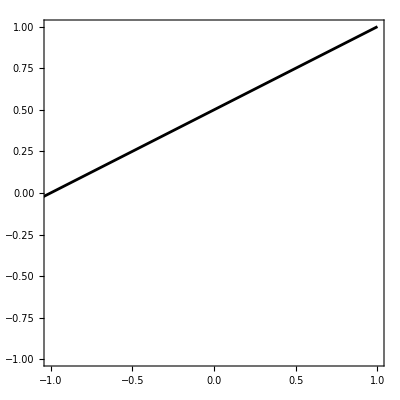
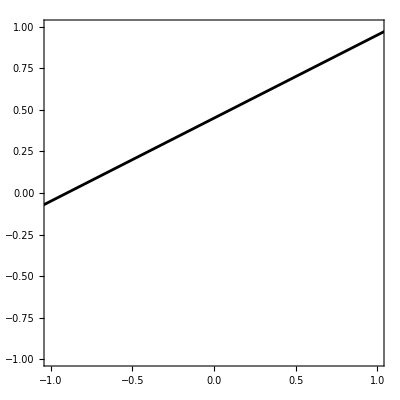
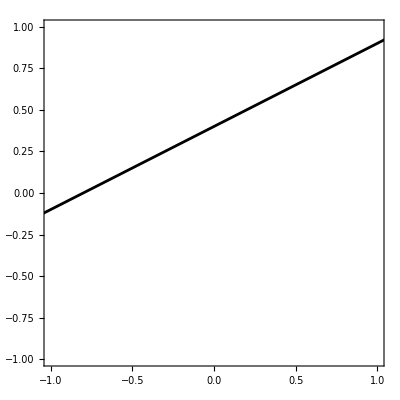
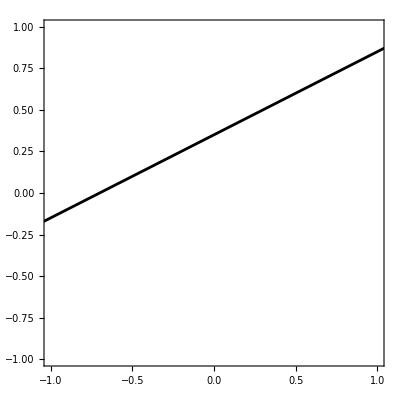
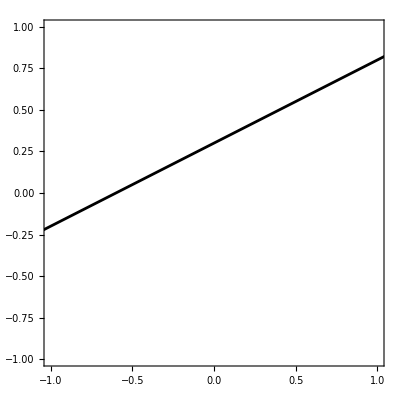
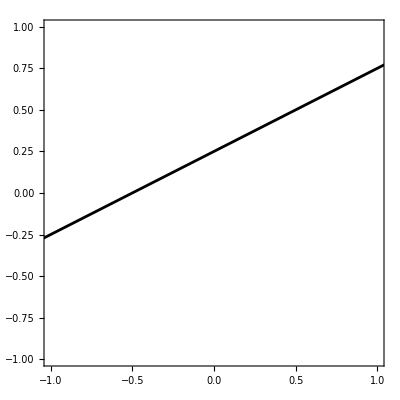
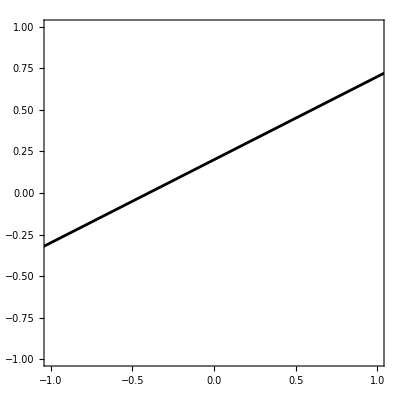
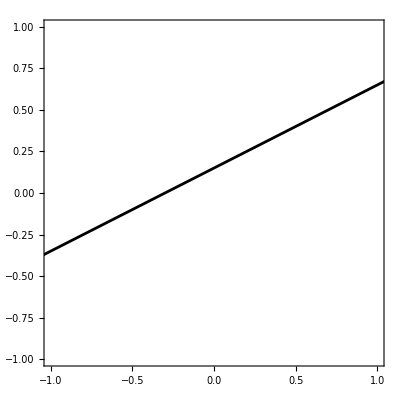

0

0.1

0.2

0.3

0.4

0.5

0.6

0.7

0.8

0.9

1.

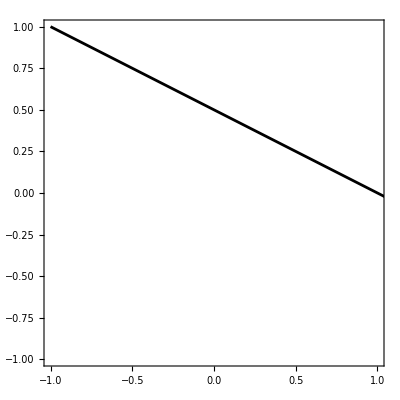
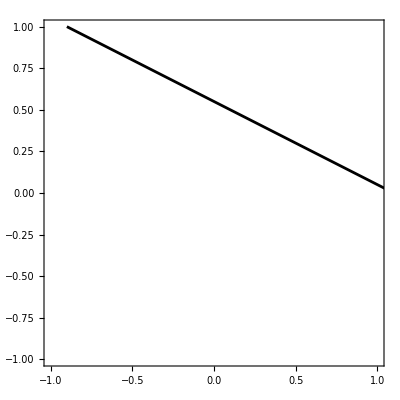
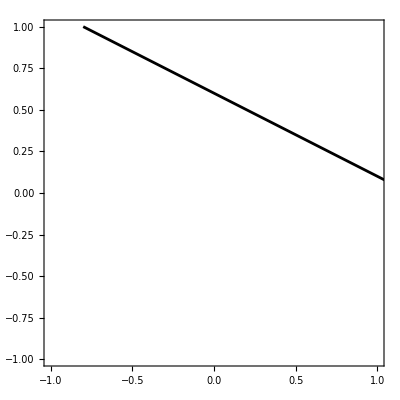
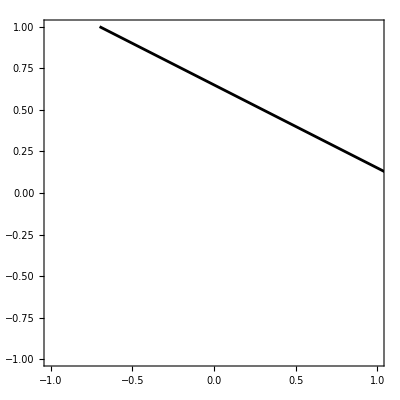
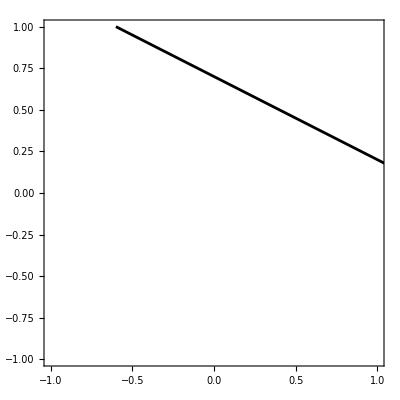
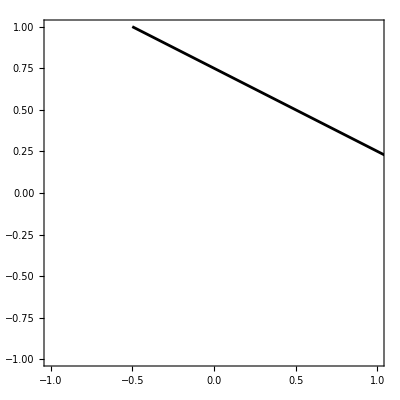
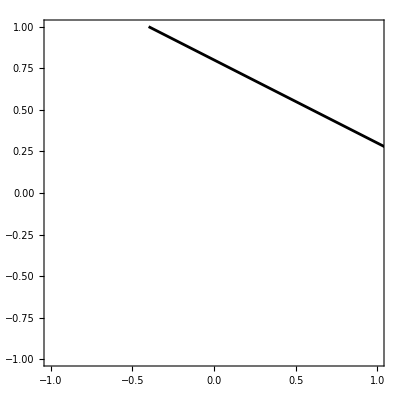
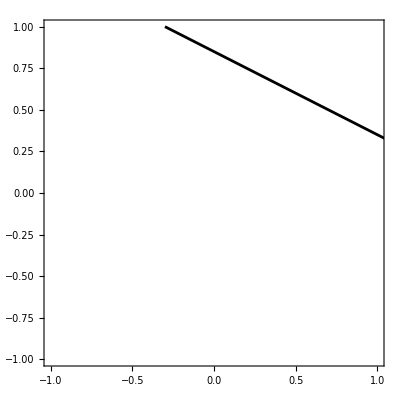

0

0.1

0.2

0.3

0.4

0.5

0.6

0.7

0.8

0.9

1.

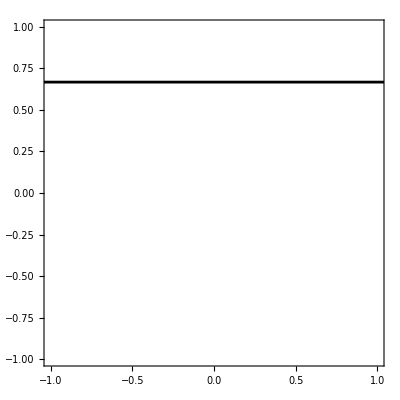
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

0

0.1

0.2

0.3

0.4

0.5

0.6

0.7

0.8

0.9

1.

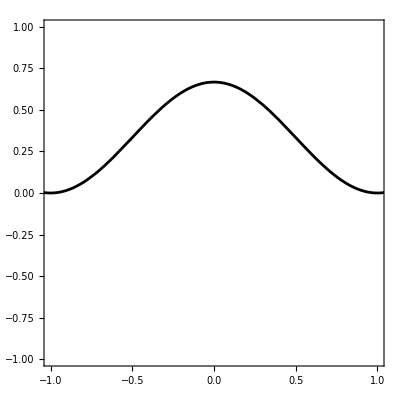
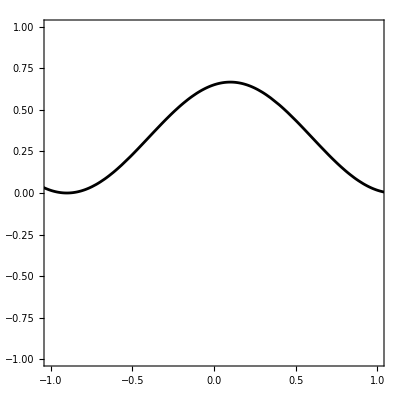
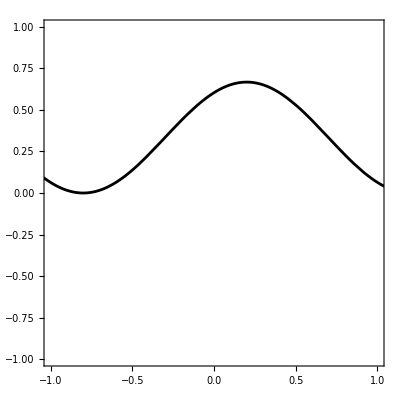
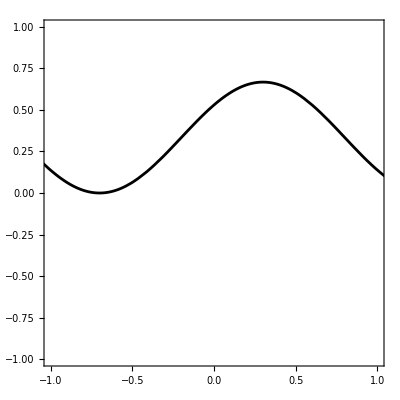
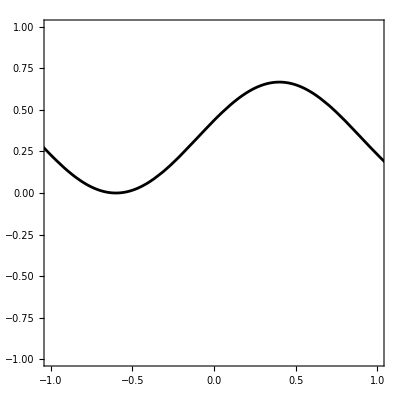
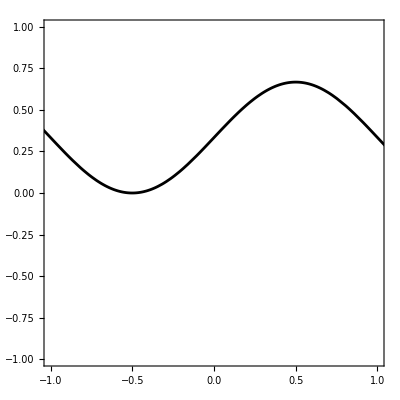
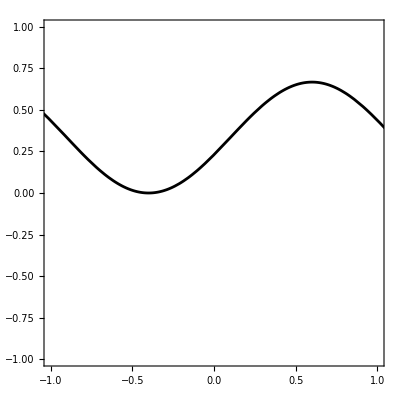
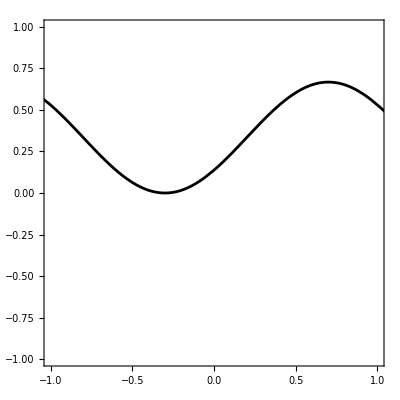

0

0.1

0.2

0.3

0.4

0.5

0.6

0.7

0.8

0.9

1.

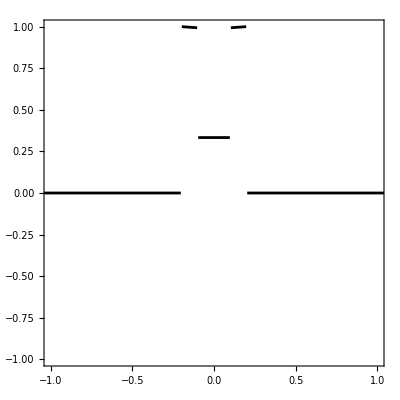
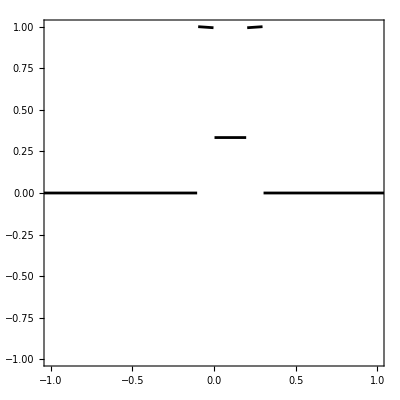
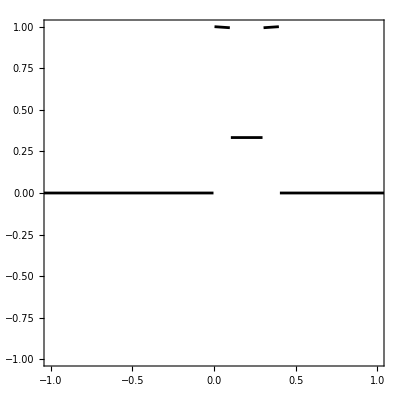
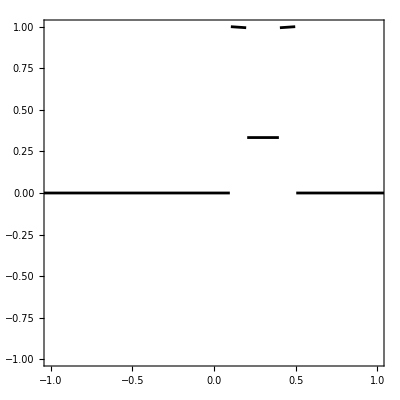
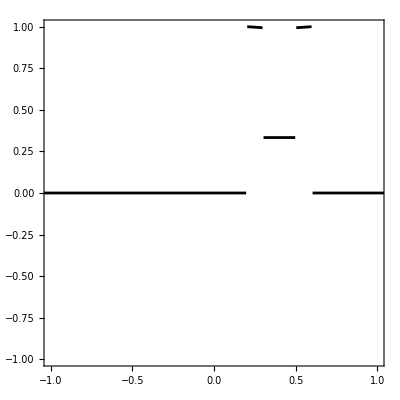
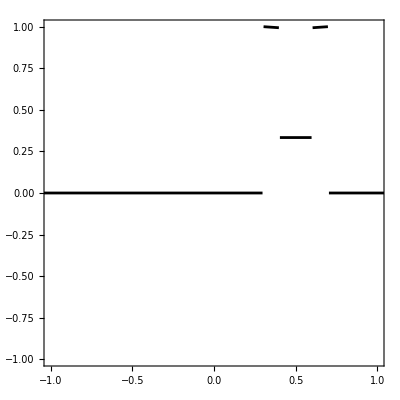
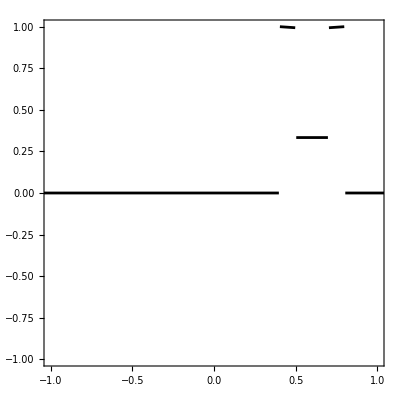
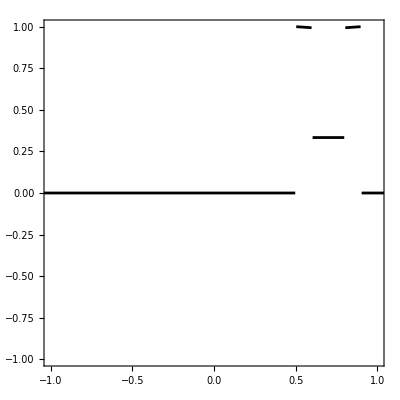

```mathematica
MakeTrainData[sol1,"C:\\Users\\gerce\\Documents\\WORK DIRECTORY\\Курсовая работа 6 сем\\КОД\\Создание датасетов\\dataset_№1\\train\\test1\\", "test1"]
MakeTrainData[sol2,"C:\\Users\\gerce\\Documents\\WORK DIRECTORY\\Курсовая работа 6 сем\\КОД\\Создание датасетов\\dataset_№1\\train\\test2\\", "test2"]
MakeTrainData[sol3,"C:\\Users\\gerce\\Documents\\WORK DIRECTORY\\Курсовая работа 6 сем\\КОД\\Создание датасетов\\dataset_№1\\train\\test3\\", "test3"]
MakeTrainData[sol4,"C:\\Users\\gerce\\Documents\\WORK DIRECTORY\\Курсовая работа 6 сем\\КОД\\Создание датасетов\\dataset_№1\\train\\test4\\", "test4"]
MakeTrainData[sol5,"C:\\Users\\gerce\\Documents\\WORK DIRECTORY\\Курсовая работа 6 сем\\КОД\\Создание датасетов\\dataset_№1\\train\\test5\\", "test5"]
```

## Создание тестовых датасетов (на основе численных решений собственной программы)